```mathematica
rhoM=0.31;
rhoR=8.4*^-5;
rhoL=1-rhoM-rhoR
```

0.689916

```mathematica
NDSolve[{D[a[t],t]^2/a[t]^2==rhoM/a[t]^3+rhoR/a[t]^4+rhoL,a[1]==1},a[t],{t,t0-10^-5,t0+10^-3}]
```

{{a[t]→InterpolatingFunction[…][t]},{a[t]→InterpolatingFunction[…][t]}}

```mathematica
{0.045079985185289086,0.045089985071617426}
```

```mathematica
an[t_]:=InterpolatingFunction[…][t]
```

```mathematica
an10[t_]:=InterpolatingFunction[…][t0+t]
```

```mathematica
anrad[t_]:=InterpolatingFunction[…][0.045079984326299796+t]
```

```mathematica
0.0450799750363528,0.1
```

```mathematica
0.04507998507161742,10.
```

```mathematica
t0=0.04507998507161742
```

0.04508

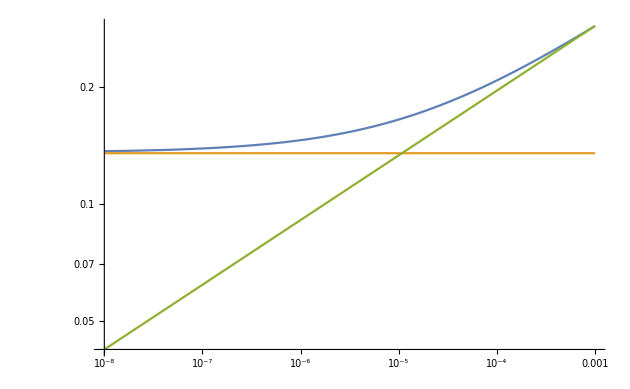

```mathematica
LogLogPlot[{anrad[t]/Sqrt[t],1/7.4,t^(1/6)/1.1},{t,10^-8,10^-3}]
```

```mathematica
1/(1+t0)*14.5
```

13.8745

```mathematica
conf10[t_]:=InterpolatingFunction[…][t]
```

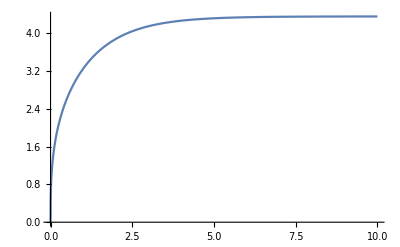

```mathematica
Plot[conf10[t],{t,0,10},PlotRange->All]
```

```mathematica
cohub10[t_]:=D[an10[t],t]
```

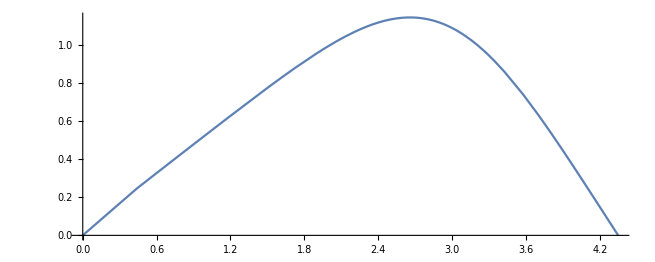

```mathematica
Show[ParametricPlot[{conf10[t],1/(InterpolatingFunction[…][0.04507998507161742+t])},{t,0,10-t0},PlotRange->All]]
```

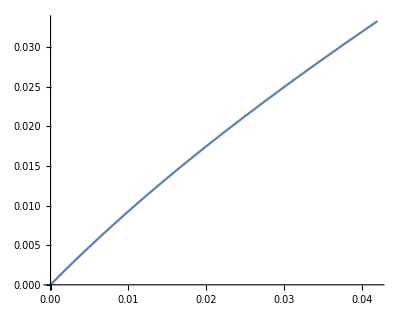

```mathematica
ParametricPlot[{conf10[t],1/(InterpolatingFunction[…][0.04507998507161742+t])},{t,0,10^-5},PlotRange->All]
```

```mathematica
1/an10[3*10^-6]
```

3776.09

```mathematica
conf10[3*10^-6]/conf10[10-t0]*63*^3
```

347.57

```mathematica
conf10[10-t0]
```

4.34889